```mathematica
(* III exterior solution *)
```

```mathematica
(* a=0 *)
```

```mathematica
Integrate[(1-1/x)/(x*(1-2/x)),x]
```

1/2 Log[2-x]+Log[x]/2

```mathematica
Simplify[(1-2/r*m)D[(e*m/r^2)/(1-(2*m)/r),r]+2/r*(1-m/r)*(e*m/r^2)/(1-(2*m)/r)]
```

0

```mathematica
Integrate[(e*m/r^2)/(1-(2*m)/r),r]
```

-e m (Log[r]/(2 m)-Log[-2 m+r]/(2 m))

```mathematica
(* a≠0 *)
```

```mathematica
(* constant ε, Subscript[r, 0]=R *)
```

```mathematica
pheqext=(1-(2*com)/x)*ph''[x]+2/x*(1-com/x)*ph'[x]-a^2*ph[x];
```

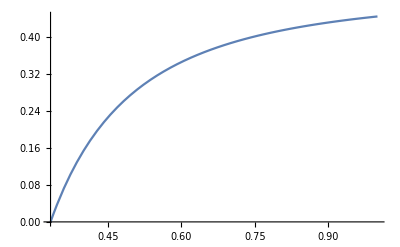

```mathematica
xr=Sqrt[1-1/(9*c^2)];Plot[1/2*xr^2,{c,1/3,1}]
```

```mathematica
com1=0.5*(1-1/(9*0.404414^2));a1=3*Sqrt[(1-1/(9*0.404414^2))]
```

1.69873

```mathematica
xinf=50
```

50

```mathematica
pheqext1=pheqext/.{com->com1,a->a1};
```

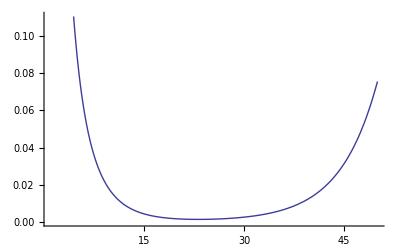

```mathematica
xmax2=50;solext=NDSolve[{pheqext1==0,ph[1]==1,ph'[1]==-1.2288},ph,{x,1,xmax2}];Plot[{Evaluate[ph[x]/.solext]},{x,1,xmax2}]
```

```mathematica
3.211711328083418/Sqrt[(1-1/(9*0.404414^2))]
```

5.67196

```mathematica
tail=100;ypl=-20;yph=-1;
yp=yph;i1=1;While[Abs[yp-N[(ypl+yph)/2]]>10^-15,yp=N[(ypl+yph)/2];sol=NDSolve[{pheqext1==0,ph[1]==0.01,ph'[1]==0.01*yp},ph,{x,1,xinf}];tail=Evaluate[ph[xinf]/.sol][[1]];Print[i1,",",NumberForm[(ypl+yph)/2,16],",",tail];If[tail>0,yph=yp,ypl=yp];i1++]
```

1,-21/2,-1.44535×10^33

2,-5.75,-5.03372×10^32

3,-3.375,-3.23821×10^31

4,-2.1875,2.03113×10^32

5,-2.78125,8.53657×10^31

6,-3.078125,2.64918×10^31

7,-3.2265625,-2.94518×10^30

8,-3.15234375,1.17733×10^31

9,-3.189453125,4.41408×10^30

10,-3.2080078125,7.34471×10^29

11,-3.21728515625,-1.10537×10^30

12,-3.212646484375,-1.85459×10^29

13,-3.2103271484375,2.74505×10^29

14,-3.21148681640625,4.45299×10^28

15,-3.212066650390625,-7.0469×10^28

16,-3.211776733398437,-1.2976×10^28

17,-3.211631774902344,1.57808×10^28

18,-3.211704254150391,1.40357×10^27

19,-3.211740493774414,-5.78654×10^27

20,-3.211722373962402,-2.192×10^27

21,-3.211713314056396,-3.94808×10^26

22,-3.211708784103394,5.05202×10^26

23,-3.211711049079895,5.55951×10^25

24,-3.211712181568146,-1.69806×10^26

25,-3.21171161532402,-5.72364×10^25

26,-3.211711332201958,-8.64169×10^23

27,-3.211711190640926,2.75742×10^25

28,-3.211711261421442,1.33848×10^25

29,-3.2117112968117,6.29506×10^24

30,-3.211711314506829,2.74781×10^24

31,-3.211711323354393,9.78362×10^23

32,-3.211711327778175,6.556×10^22

33,-3.211711329990067,-3.9851×10^23

34,-3.211711328884121,-1.72467×10^23

35,-3.211711328331148,-5.54609×10^22

36,-3.211711328054662,4.79329×10^21

37,-3.211711328192905,-2.57101×10^22

38,-3.211711328123783,-1.06707×10^22

39,-3.211711328089223,-7.59872×10^21

40,-3.211711328071942,8.64831×10^20

41,-3.211711328080582,6.32443×10^20

42,-3.211711328084903,-4.97371×10^21

43,-3.211711328082743,8.27871×10^20

44,-3.211711328083823,-4.18457×10^21

45,-3.211711328083283,9.4727×10^20

46,-3.211711328083553,-4.08835×10^21

47,-3.211711328083418,9.31128×10^20

48,-3.211711328083485,-4.06562×10^21

49,-3.211711328083451,-4.05367×10^21

50,-3.211711328083434,-4.04936×10^21

51,-3.211711328083426,-4.04558×10^21

52,-3.211711328083422,-4.04279×10^21

53,-3.21171132808342,-4.04258×10^21

54,-3.211711328083418,9.29375×10^20

```mathematica
"-5.328947908158261"
```

```mathematica
a1=1
```

1

```mathematica
Npt=1000;comset=Table[0.01+((i-1)*(0.43-0.01))/(Npt-1),{i,1,Npt}];ypn=Table[0,{i,1,Npt}];
```

```mathematica
xinf=50
```

50

```mathematica
Do[pheqext1=pheqext/.{a->a1,com->comset[[i]]};tail=100;ypl=-20;yph=-1;
yp=yph;While[Abs[yp-N[(ypl+yph)/2]]>10^-9,yp=N[(ypl+yph)/2];sol=NDSolve[{pheqext1==0,ph[1]==1,ph'[1]==yp},ph,{x,1,xinf}];tail=Evaluate[ph[xinf]/.sol][[1]];If[tail>0,yph=yp,ypl=yp]];ypn[[i]]=(ypl+yph)/2,{i,1,Npt}]
```

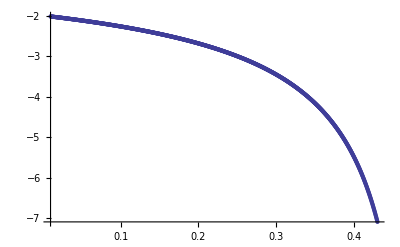

```mathematica
ListPlot[Table[{comset[[i]],ypn[[i]]},{i,1,Npt}],PlotRange->All]
```

```mathematica
ypn1=ypn;
```

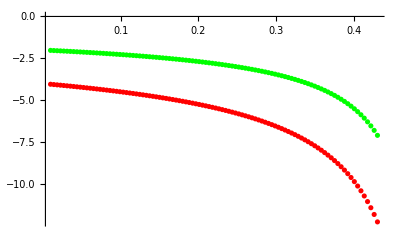

```mathematica
ListPlot[{Table[{comset[[i]],ypn[[i]]},{i,1,Npt}],Table[{comset[[i]],ypn1[[i]]},{i,1,Npt}]},PlotRange->All,PlotStyle->{Red,Green}]
```

```mathematica
(* real neutron star, Subscript[r, 0]=10^6 cm *)
```

```mathematica
pheqex=(1-(2*mr0)/x)*ph''[x]+2/x*(1-mr0/x)*ph'[x]-a^2*ph[x]
```

-a^2 ph[x]+(2 (1-mr0/x) ph'[x])/x+(1-(2 mr0)/x) ph''[x]

```mathematica
DSolve[pheqex==0,ph[x],x]
```

{{ph[x]→DifferentialRoot[Function[{y,x},{-x^2 a^2 y[x]+(2 x-2 mr0) y'[x]+(x^2-2 x mr0) y''[x]==0,y[1]==C[1],y'[1]==C[2]}]][x]}}

```mathematica
a1=1.287878787878788
```

1.28788

```mathematica
mr01=mdata[[1]]
```

0.0227451

```mathematica
pheqex1=pheqex/.{mr0->mr01,a->a1};xmin=rdata[[1]]
```

1.94196

```mathematica
xinf=50
```

50

```mathematica
solex=NDSolve[{pheqex1==0,ph[xmin]==1,ph'[xmin]==-1},ph,{x,xmin,xinf}];Plot[Evaluate[ph[x]/.solex],{x,xmin,xinf}]
```

-Graphics-

```mathematica
tail=Evaluate[ph[xinf]/.solex][[1]]
```

-6.46158×10^18

```mathematica
tail=100;ypl=-20;yph=-1;
yp=yph;Ntot=1000;i1=1;While[Abs[yp-N[(ypl+yph)/2]]>10^-15&&i1<Ntot,yp=N[(ypl+yph)/2];sol=NDSolve[{pheqex1==0,ph[xmin]==1,ph'[xmin]==yp},ph,{x,xmin,xinf}];tail=Evaluate[ph[xinf]/.sol][[1]];Print[i1,",",NumberForm[(ypl+yph)/2,16],",",tail];If[tail>0,yph=yp,ypl=yp];i1++]
```

1,-21/2,-1.07359×10^26

2,-5.75,-4.85942×10^25

3,-3.375,-1.92121×10^25

4,-2.1875,-4.52103×10^24

5,-1.59375,2.82451×10^24

6,-1.890625,-8.48261×10^23

7,-1.7421875,9.88124×10^23

8,-1.81640625,6.99316×10^22

9,-1.853515625,-3.89165×10^23

10,-1.8349609375,-1.59616×10^23

11,-1.82568359375,-4.48425×10^22

12,-1.821044921875,1.25446×10^22

13,-1.8233642578125,-1.61489×10^22

14,-1.82220458984375,-1.80219×10^21

15,-1.821624755859375,5.37119×10^21

16,-1.821914672851562,1.7845×10^21

17,-1.822059631347656,-8.84154×10^18

18,-1.821987152099609,8.87834×10^20

19,-1.822023391723633,4.39496×10^20

20,-1.822041511535645,2.15327×10^20

21,-1.82205057144165,1.03243×10^20

22,-1.822055101394653,4.72016×10^19

23,-1.822057366371155,1.91803×10^19

24,-1.822058498859406,5.16953×10^18

25,-1.822059065103531,-1.83607×10^18

26,-1.822058781981468,1.66679×10^18

27,-1.8220589235425,-8.46643×10^16

28,-1.822058852761984,7.91093×10^17

29,-1.822058888152242,3.53245×10^17

30,-1.822058905847371,1.34311×10^17

31,-1.822058914694935,2.48529×10^16

32,-1.822058919118717,-2.99142×10^16

33,-1.822058916906826,-2.53787×10^15

34,-1.822058915800881,1.11629×10^16

35,-1.822058916353853,4.31693×10^15

36,-1.82205891663034,8.96507×10^14

37,-1.822058916768583,-8.23514×10^14

38,-1.822058916699461,3.69734×10^13

39,-1.822058916734022,-3.94156×10^14

40,-1.822058916716742,-1.79161×10^14

41,-1.822058916708102,-7.14737×10^13

42,-1.822058916703782,-1.80684×10^13

43,-1.822058916701621,9.74938×10^12

44,-1.822058916702701,-4.14354×10^12

45,-1.822058916702161,2.99242×10^12

46,-1.822058916702431,-6.22916×10^11

47,-1.822058916702296,1.20465×10^12

48,-1.822058916702364,2.96017×10^11

49,-1.822058916702398,-1.62982×10^11

50,-1.822058916702381,6.16769×10^10

51,-1.822058916702389,-4.47931×10^10

52,-1.822058916702385,1.18244×10^10

53,-1.822058916702387,-1.7602×10^10

```mathematica
tail=100;ypl=-20;yph=-1;
yp=yph;Ntot=1000;i1=1;While[Abs[yp+N[Sqrt[ypl*yph]]]>10^-15&&i1<Ntot,yp=-N[Sqrt[ypl*yph]];sol=NDSolve[{pheqex1==0,ph[xmin]==1,ph'[xmin]==yp},ph,{x,xmin,xinf}];tail=Evaluate[ph[xinf]/.sol][[1]];Print[i1,",",NumberForm[-N[Sqrt[ypl*yph]],16],",",tail];If[tail>0,yph=yp,ypl=yp];i1++]
```

1,-4.47213595499958,-3.62203×10^25

2,-2.114742526881128,-3.97419×10^24

3,-1.454215433448954,5.06097×10^24

4,-1.753650826236904,9.65085×10^23

5,-1.925751795934099,-1.38904×10^24

6,-1.837687739543101,-1.84433×10^23

7,-1.795177602025824,3.97051×10^23

8,-1.816308307954694,1.0801×10^23

9,-1.82696675086292,-3.77837×10^22

10,-1.82162973404293,3.52199×10^22

11,-1.824296290759727,-1.25515×10^21

12,-1.822962524834821,1.69891×10^22

13,-1.823629285861068,7.86863×10^21

14,-1.823962757820772,3.30716×10^21

15,-1.824129516667146,1.02611×10^21

16,-1.824212901807573,-1.14494×10^20

17,-1.824171208760905,4.55815×10^20

18,-1.824192055165124,1.70663×10^20

19,-1.82420247845657,2.80852×10^19

20,-1.824207690124627,-4.32051×10^19

21,-1.824205084288737,-7.56028×10^18

22,-1.824203781372189,1.02626×10^19

23,-1.824204432830347,1.35127×10^18

24,-1.824204758559513,-3.10458×10^18

25,-1.824204595694922,-8.76689×10^17

26,-1.824204514262633,2.37319×10^17

27,-1.824204554978777,-3.19693×10^17

28,-1.824204534620705,-4.12068×10^16

29,-1.824204524441669,9.80707×10^16

30,-1.824204529531187,2.84582×10^16

31,-1.824204532075946,-6.37778×10^15

32,-1.824204530803566,1.10436×10^16

33,-1.824204531439756,2.34043×10^15

34,-1.824204531757851,-2.02785×10^15

35,-1.824204531598804,1.57039×10^14

36,-1.824204531678327,-9.37219×10^14

37,-1.824204531638565,-3.91029×10^14

38,-1.824204531618684,-1.17372×10^14

39,-1.824204531608744,2.02232×10^13

40,-1.824204531613714,-4.9863×10^13

41,-1.824204531611229,-1.49912×10^13

42,-1.824204531609986,2.93611×10^12

43,-1.824204531610608,-6.04685×10^12

44,-1.824204531610297,-1.61562×10^12

45,-1.824204531610142,6.65522×10^11

46,-1.824204531610219,-5.1208×10^11

47,-1.82420453161018,7.60756×10^10

48,-1.8242045316102,-2.206×10^11

49,-1.82420453161019,-7.10816×10^10

50,-1.824204531610185,1.0296×10^10

51,-1.824204531610188,-3.92782×10^10

52,-1.824204531610186,-8.82983×10^9

```mathematica
Gg=6.67408*10^-8;spdl=29979245800.0;lch=10^6;SetDirectory["~/Documents/research/kiaa/stns/STG"];
```

```mathematica
data=ReadList["TOVhpc.txt",Number];Npt=Length[data]/4;mdata=Table[0,{i,1,Npt}];rdata=Table[0,{i,1,Npt}];Do[mdata[[i]]=(data[[2+(i-1)*4]]*Gg)/(spdl^2*lch);rdata[[i]]=data[[3+(i-1)*4]]/lch,{i,1,Npt}];Npt
```

1000

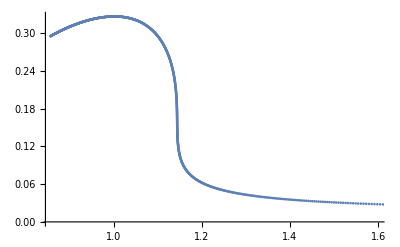

```mathematica
ListPlot[Table[{rdata[[i]],mdata[[i]]},{i,1,Npt}]]
```

```mathematica
mdata[[10]]
```

0.295352

```mathematica
xmin=rdata[[1]]
```

1.94196

```mathematica
a1=1.29
```

1.29

```mathematica
pheqex1=pheqex/.{a->a1,mr0->mdata[[1]]};solex=NDSolve[{pheqex1==0,ph[xmin]==1,ph'[xmin]==-4},ph,{x,xmin,xinf}];Plot[Evaluate[ph[x]/.solex],{x,xmin,xinf}]
```

-Graphics-

```mathematica
(* 9min4s for Npt=1000 *)
```

```mathematica
a1=2
```

2

```mathematica
xinf=50
```

50

```mathematica
ypn=Table[0,{i,1,Npt}];Do[pheqex1=pheqex/.{a->a1,mr0->mdata[[i]]};xmin=rdata[[i]];tail=100;ypl=-20;yph=-1;
yp=yph;While[Abs[yp-N[(ypl+yph)/2]]>10^-9,yp=N[(ypl+yph)/2];sol=NDSolve[{pheqex1==0,ph[xmin]==1,ph'[xmin]==yp},ph,{x,xmin,xinf}];tail=Evaluate[ph[xinf]/.sol][[1]];If[tail>0,yph=yp,ypl=yp]];ypn[[i]]=(ypl+yph)/2,{i,1,Npt}]
```

```mathematica
mdata[[1]]/rdata[[1]]
```

0.0117124

```mathematica
ypn[[45]]
```

-3.69919

```mathematica
Do[ypn[[i]]>>>"ypextdata2.txt",{i,1,Npt}]
```

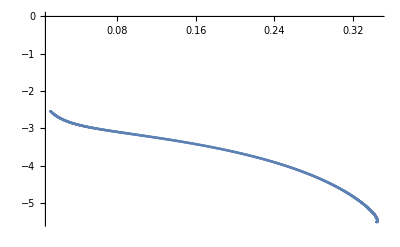

```mathematica
ListPlot[Table[{mdata[[i]]/rdata[[i]],ypn[[i]]},{i,1,Npt}],PlotRange->All]
```

```mathematica
ypn1=ypn;
```

```mathematica
ypn2=ypn;
```

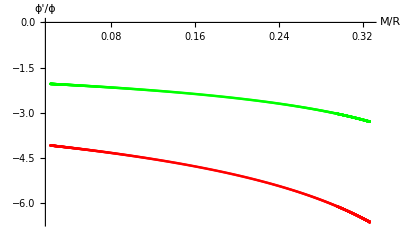

```mathematica
ListPlot[{Table[{mdata[[i]],ypn2[[i]]},{i,1,Npt}],Table[{mdata[[i]],ypn1[[i]]},{i,1,Npt}]},PlotStyle->{Red,Green},AxesLabel->{"M/R",(ϕ'(R))/(ϕ(R))},PlotRange->All]
```